```mathematica
vols={0.01,0.008,0.011,0.008}; (*хз что, но как будто что-то по типа среднего*)
crl=({{1, 0.35, 0.45, 0.36}, {0.35, 1, 0.43, 0.32}, {0.45, 0.43, 1, 0.46}, {0.36, 0.32, 0.46, 1}}); (*кросс-корреляции четырёх рядов*)
cm=Table[vols[[i]]*vols[[j]]*crl[[i,j]],{i,1,Length[vols]},{j,1,Length[vols]}] (* корреляционная матрица *)
```

{{0.0001,0.000028,0.0000495,0.0000288},{0.000028,0.000064,0.00003784,0.00002048},{0.0000495,0.00003784,0.000121,0.00004048},{0.0000288,0.00002048,0.00004048,0.000064}}

{{0.55,0.72,1.25,1},{0.54453,0.719201,1.25756,0.999969},1497,{0.372235,0.911987,0.690265,1.20275},{0.375398,0.901029,0.693003,1.19962}}
 |  |  |  |

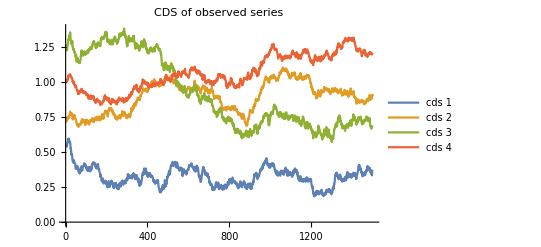

```mathematica
init={0.55,0.72,1.25,1}; (*начальные значения, с которых стартуют ряды*)
mn=MultinormalDistribution[{0,0,0,0},cm];
data=Accumulate[Prepend[RandomVariate[mn,1500],init]](* подгружаем в первую ячейку начальные значения, а дальше генерируются последовательности из 1500 случайных чисел, распределённых по многомерному гауссу с нулевым средним и корреляционной матрицей из предыдущего селла. Аккумулейт просто вставляет новый набор из 4 чисел в массив *)
ListLinePlot[Transpose[data],PlotLegends->{"cds 1","cds 2","cds 3", "cds 4"},PlotLabel->Style["CDS of observed series",15]]
```

```mathematica
traindata=data[[;;600]];
validata=data[[601;;900]];
testdata=data[[901;;]];
```

```mathematica
trainset=Table[Drop[traindata,None,-1][[i]]->Flatten[Take[traindata,All,-1]][[i]],{i,1,Length[traindata]}];(*таблица вида (первое второе третье)-> (четвёртое). Флаттен делает вместо {number} просто number *)
testset=Table[Drop[testdata,None,-1][[i]]->Flatten[Take[testdata,All,-1]][[i]],{i,1,Length[testdata]}];
validset=Table[Drop[validata,None,-1][[i]]->Flatten[Take[validata,All,-1]][[i]],{i,1,Length[validata]}];
```

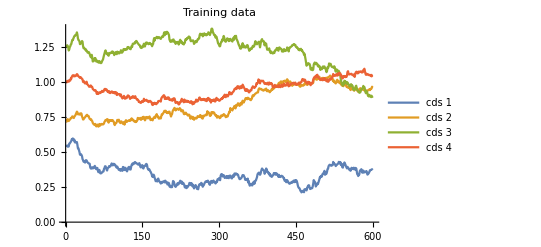
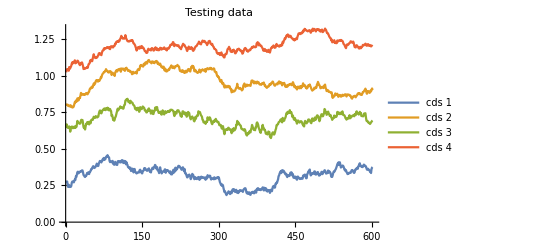
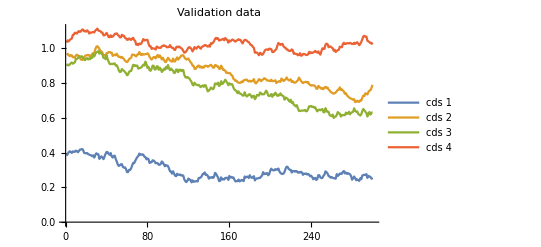

```mathematica
{ListLinePlot[Transpose[traindata],PlotLegends->{"cds 1","cds 2","cds 3", "cds 4"},PlotLabel->Style["Training data",15]],ListLinePlot[Transpose[testdata],PlotLegends->{"cds 1","cds 2","cds 3", "cds 4"},PlotLabel->Style["Testing data",15]],ListLinePlot[Transpose[validata],PlotLegends->{"cds 1","cds 2","cds 3", "cds 4"},PlotLabel->Style["Validation data",15]]}
```

```mathematica
pred=Predict[trainset,ValidationSet->validset,Method->"RandomForest",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
PredictorInformation[pred]
```

Predictor information
Input type | NumericalVector (length: 3)
Method | RandomForest
Standard deviation | 0.0394 ± 0.0011
Loss | 0.59 ± 0.23
Evaluation time | 47.4 µs/example
Predictor memory | 334. kB
Training examples used | 600 examples
Training time | 1.61 s
 |

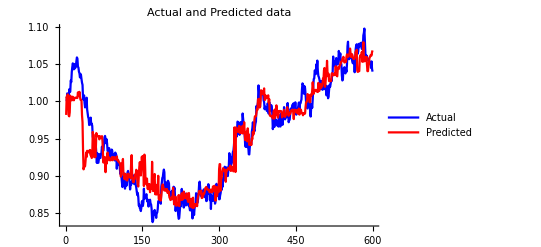

```mathematica
plotdata=Drop[traindata,None,-1];
adata=Transpose[Take[traindata,All,-1]]//Flatten;
pdata=Table[pred[plotdata[[i]]],{i,1,Length[traindata]}];
ListLinePlot[{adata,pdata},PlotLabel->Style["Actual and Predicted data",15],PlotLegends->{"Actual","Predicted"},PlotStyle->{Blue,Red}]
```

```mathematica
pm=PredictorMeasurements[pred,testset]
```

PredictorMeasurementsObject[…]

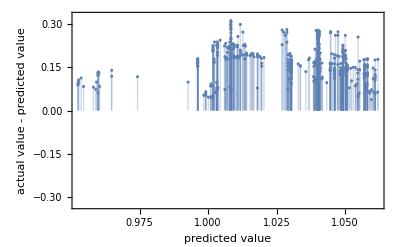

```mathematica
pm["ResidualPlot"]
```

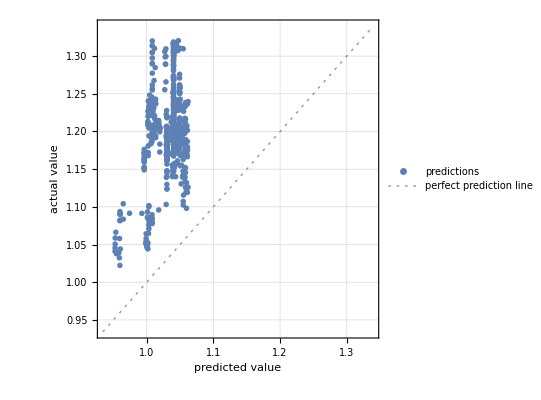

```mathematica
pm["ComparisonPlot"]
```

```mathematica
tvols={0.015,0.02,0.03};
tcorr=({{1, 0.4, 0.5}, {0.4, 1, 0.45}, {0.5, 0.45, 1}});
tcm=Table[tvols[[i]]*tvols[[j]]*tcorr[[i,j]],{i,1,Length[tvols]},{j,1,Length[tvols]}]
```

{{0.000225,0.00012,0.000225},{0.00012,0.0004,0.00027},{0.000225,0.00027,0.0009}}

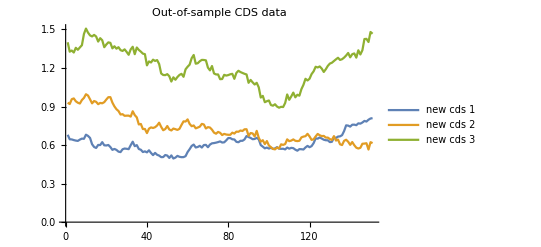

```mathematica
newinit={0.68,0.93,1.4};
mn=MultinormalDistribution[{0,0,0},tcm];
tdata=Accumulate[Prepend[RandomVariate[mn,150],newinit]];
ListLinePlot[Transpose[tdata],PlotLegends->{"new cds 1","new cds 2","new cds 3"},PlotLabel->Style["Out-of-sample CDS data",15]]
```

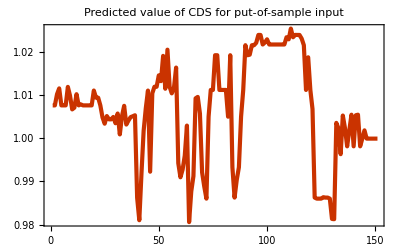

```mathematica
newdata=Table[pred[tdata[[i]]],{i,1,Length[tdata]}];
ListLinePlot[newdata, PlotTheme->"Web", PlotRange->All,PlotLabel->Style["Predicted value of CDS for put-of-sample input",15]]
```

```mathematica
edist=SmoothKernelDistribution[newdata]
```

DataDistribution[…]

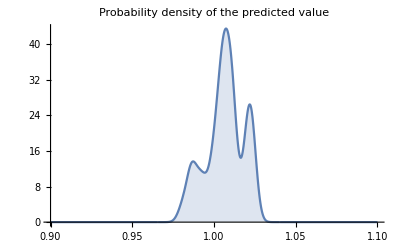

```mathematica
Plot[PDF[edist,x],{x,0.9,1.1},PlotLabel->"Probability density of the predicted value", Filling->Axis,PlotRange->All]
```

```mathematica
stats={Mean,Median,Variance,Min,Max,Skewness,Kurtosis};
TableForm[Through[stats[newdata]],TableHeadings->{stats,None}]
```

Mean | 1.00663
Median | 1.00767
Variance | 0.000131629
Min | 0.980555
Max | 1.0255
Skewness | -0.364676
Kurtosis | 2.47768

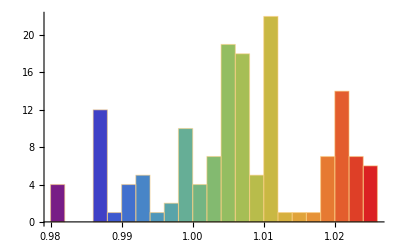

```mathematica
Histogram[newdata,25,ChartStyle->"Rainbow"]
```

```mathematica
pneural=Predict[trainset,ValidationSet->validset,Method->"NeuralNetwork",PerformanceGoal->"Speed"]
```

PredictorFunction[…]

```mathematica
p=Predict[trainset,ValidationSet->validset,Method->"RandomForest",PerformanceGoal->"Speed"]
```

PredictorFunction[…]

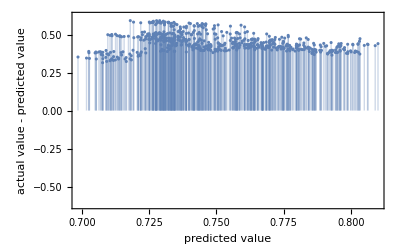

```mathematica
pneuraltest=PredictorMeasurements[pneural,testset];
pneuraltest["ResidualPlot"]
```

```mathematica
pneural[Drop[init,-1],"Distribution"]
```

NormalDistribution[0.804305,0.023857]

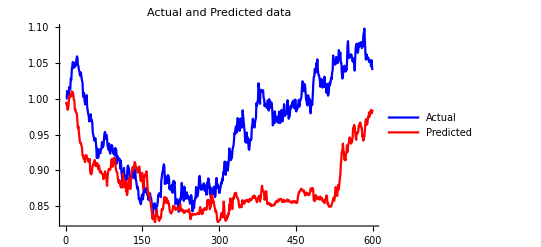

```mathematica
pdata=Table[1.8-pneural[plotdata[[i]]],{i,1,Length[traindata]}];
ListLinePlot[{adata,pdata},PlotLabel->Style["Actual and Predicted data",15],PlotLegends->{"Actual","Predicted"},PlotStyle->{Blue,Red}]
```

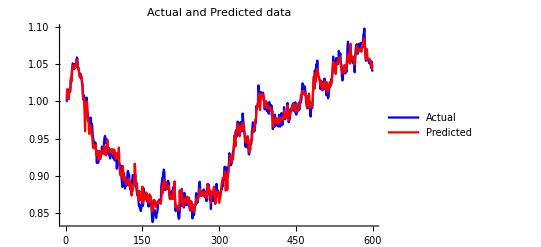

```mathematica
pdata=Table[p[plotdata[[i]]],{i,1,Length[traindata]}];
ListLinePlot[{adata,pdata},PlotLabel->Style["Actual and Predicted data",15],PlotLegends->{"Actual","Predicted"},PlotStyle->{Blue,Red}]
```